```mathematica
jake=1/(2b) * {{b+1,b-1},{b-1,b+1}}
```

{{(1+b)/(2 b),(-1+b)/(2 b)},{(-1+b)/(2 b),(1+b)/(2 b)}}

```mathematica
Eigenvectors[jake]
```

{{1,1},{-1,1}}

```mathematica
pool[b_]:=1/(6b^2)*{{b^2+3b+2,4b^2-4 ,b^2-3b+2},
{b^2-1, 4b^2+2,b^2-1},
{b^2-3b+2,4b^2-4,b^2+3b+2}}
```

```mathematica
Clear[pool]
```

```mathematica
MatrixForm[pool[3]]
```

(10/27 | 16/27 | 1/27
4/27 | 19/27 | 4/27
1/27 | 16/27 | 10/27)

```mathematica
Eigenvectors[pool[7]]
```

{{1,1,1},{-1,0,1},{1,-1/2,1}}

```mathematica
Fred[i_,j_,b_,m_]:=b^(-m) Sum[(-1)^r *Binomial[m+1,r]
* Binomial[m-1-i+(j+1-r)b,m],{r,0,j-Quotient[i,b]}]
```

```mathematica
FredTable[b_,m_] := Table[N[Fred[i,j,b,m]],{i,0,m-1},{j,0,m-1}]
```

```mathematica
Animate[ListPlot3D[1/FredTable[i,23],ImageSize->500],{i,Prime[Range[1,25]]}]
```

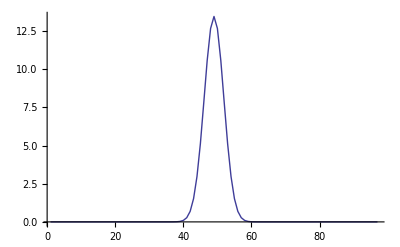

```mathematica
ListLinePlot[Map[Sum[i,{i,#}]&,Transpose[FredTable[97,97]]],PlotRange->All]
```

```mathematica
Limit[Diagonal[FredTable[i,97]],i->Infinity]
```

Power::infy: Infinite expression 1/0^97 encountered.

Quotient::divz: The argument 0 in Quotient[0, 0] should be nonzero.

General::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Floor[1 - Quotient[0, 0]].

∞::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^97 encountered.

Quotient::divz: The argument 0 in Quotient[0, 0] should be nonzero.

General::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Floor[2 - Quotient[0, 0]].

∞::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^97 encountered.

General::stop: Further output of Power will be suppressed during this calculation.

Quotient::divz: The argument 0 in Quotient[0, 0] should be nonzero.

General::stop: Further output of Quotient will be suppressed during this calculation.

General::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Floor[3 - Quotient[0, 0]].

General::stop: Further output of General will be suppressed during this calculation.

∞::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of indet will be suppressed during this calculation.

{Indeterminate,1.,9.59861×10^-25,1.41806×10^-35,6.11744×10^-41,2.10415×10^-43,3.62962×10^-44,6.92507×10^-44,5.95185×10^-43,1.31469×10^-41,5.19647×10^-40,2.89509×10^-38,1.9378×10^-36,1.3987×10^-34,1.01147×10^-32,6.96896×10^-31,4.42056×10^-29,2.52219×10^-27,1.27439×10^-25,5.64449×10^-24,2.17751×10^-22,7.28931×10^-21,2.11347×10^-19,5.30464×10^-18,1.153×10^-16,2.17244×10^-15,3.5533×10^-14,5.05368×10^-13,6.26143×10^-12,6.77109×10^-11,6.40319×10^-10,5.3053×10^-9,3.85831×10^-8,2.46729×10^-7,1.38964×10^-6,6.9042×10^-6,0.0000303028,0.000117647,0.000404512,0.0012331,0.00333573,0.00801436,0.0171131,0.0324952,0.0548943,0.0825248,0.110425,0.13152,0.139417,0.131504,0.110331,0.0822934,0.0545315,0.0320763,0.0167318,0.00773059,0.00315942,0.00114039,0.000362898,0.000101612,0.0000249782,5.37726×10^-6,1.01096×10^-6,1.6548×10^-7,2.35019×10^-8,2.885×10^-9,3.04815×10^-10,2.75881×10^-11,2.12774×10^-12,1.39021×10^-13,7.64458×10^-15,3.51192×10^-16,1.33677×10^-17,4.17668×10^-19,1.0599×10^-20,2.15831×10^-22,3.47835×10^-24,4.36643×10^-26,4.19132×10^-28,3.01073×10^-30,1.57779×10^-32,5.85264×10^-35,1.48188×10^-37,2.45063×10^-40,2.50722×10^-43,1.48311×10^-46,4.656×10^-50,6.94617×10^-54,4.25893×10^-58,8.82611×10^-63,4.71511×10^-68,4.39871×10^-74,3.98115×10^-81,1.35474×10^-89,3.22631×10^-100,1.70016×10^-114,1.87358×10^-136}

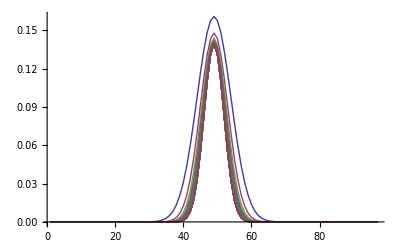

```mathematica
ListLinePlot[Table[Diagonal[FredTable[i,97]],{i,2,50}], PlotRange->All]
```

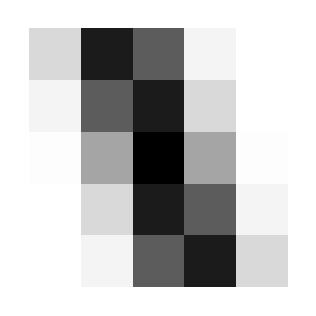

```mathematica
ArrayPlot[MapAll[Map[N[#]&,#]&,FredTable[3,5]]];ArrayPlot[MapAll[Map[N[#]&,#]&,FredTable[5,5]]]
```

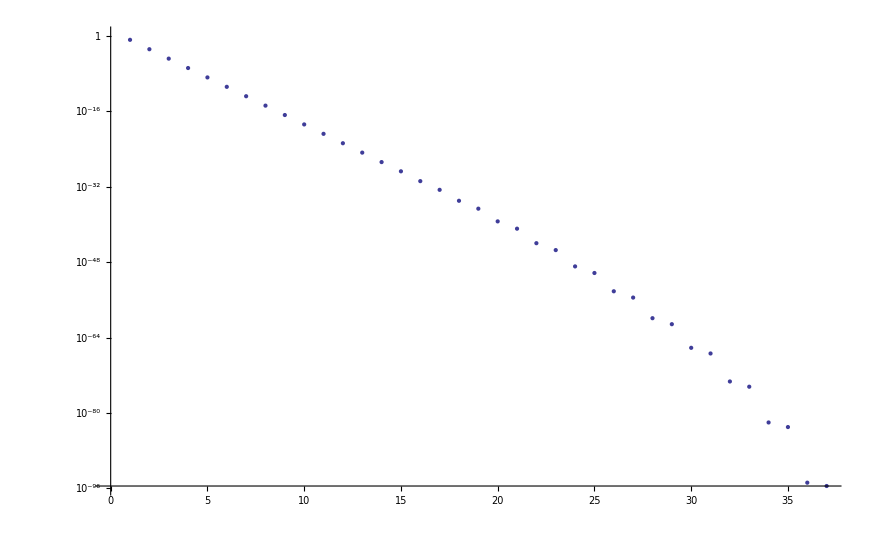

```mathematica
ListLogPlot[N[Eigenvalues[FredTable[101,37]*FredTable[97,37]]]]
```

```mathematica
MatrixForm[
With[
{m=3,b=a},
Table[Fred[i,j,b,m],{i,0,m-1},{j,0,m-1}]
]
]
```

(-((-1)^(-Quotient[0,a]) Binomial[4,1-Quotient[0,a]] (-1+Quotient[0,a]) (6+9 a+3 a^2+8 Quotient[0,a]+30 a Quotient[0,a]+28 a^2 Quotient[0,a]+18 a Quotient[0,a]^2+36 a^2 Quotient[0,a]^2+12 a^2 Quotient[0,a]^3))/(72 a^2) | ((-1)^(-Quotient[0,a]) Binomial[4,2-Quotient[0,a]] (-2+Quotient[0,a]) (2-2 a^2+4 Quotient[0,a]+9 a Quotient[0,a]-a^2 Quotient[0,a]+9 a Quotient[0,a]^2+9 a^2 Quotient[0,a]^2+6 a^2 Quotient[0,a]^3))/(36 a^2) | -((-1)^(-Quotient[0,a]) Binomial[4,3-Quotient[0,a]] (-3+Quotient[0,a]) (2-3 a+a^2+8 Quotient[0,a]+6 a Quotient[0,a]-8 a^2 Quotient[0,a]+18 a Quotient[0,a]^2+12 a^2 Quotient[0,a]^3))/(72 a^2)
-((-1)^(-Quotient[1,a]) Binomial[4,1-Quotient[1,a]] (-1+Quotient[1,a]) (-3+3 a^2-4 Quotient[1,a]+28 a^2 Quotient[1,a]+36 a^2 Quotient[1,a]^2+12 a^2 Quotient[1,a]^3))/(72 a^2) | ((-1)^(-Quotient[1,a]) Binomial[4,2-Quotient[1,a]] (-2+Quotient[1,a]) (1+2 Quotient[1,a]) (-1-2 a^2+3 a^2 Quotient[1,a]+3 a^2 Quotient[1,a]^2))/(36 a^2) | -((-1)^(-Quotient[1,a]) Binomial[4,3-Quotient[1,a]] (-3+Quotient[1,a]) (-1+a^2-4 Quotient[1,a]-8 a^2 Quotient[1,a]+12 a^2 Quotient[1,a]^3))/(72 a^2)
-((-1)^(-Quotient[2,a]) Binomial[4,1-Quotient[2,a]] (-1+Quotient[2,a]) (6-9 a+3 a^2+8 Quotient[2,a]-30 a Quotient[2,a]+28 a^2 Quotient[2,a]-18 a Quotient[2,a]^2+36 a^2 Quotient[2,a]^2+12 a^2 Quotient[2,a]^3))/(72 a^2) | ((-1)^(-Quotient[2,a]) Binomial[4,2-Quotient[2,a]] (-2+Quotient[2,a]) (2-2 a^2+4 Quotient[2,a]-9 a Quotient[2,a]-a^2 Quotient[2,a]-9 a Quotient[2,a]^2+9 a^2 Quotient[2,a]^2+6 a^2 Quotient[2,a]^3))/(36 a^2) | -((-1)^(-Quotient[2,a]) Binomial[4,3-Quotient[2,a]] (-3+Quotient[2,a]) (2+3 a+a^2+8 Quotient[2,a]-6 a Quotient[2,a]-8 a^2 Quotient[2,a]-18 a Quotient[2,a]^2+12 a^2 Quotient[2,a]^3))/(72 a^2))

```mathematica
ListPlot3D[
Eigenvectors[With[
{m=97,b=2},
Table[Fred[i,j,b,m],{i,0,m-1},{j,0,m-1}]
]],
PlotRange->All
]
```

-Graphics3D-

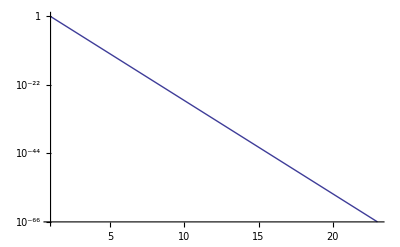

```mathematica
ListLogPlot[
Eigenvalues[With[
{m=23,b=997},
Table[Fred[i,j,b,m],{i,0,m-1},{j,0,m-1}]
]],
PlotRange->All, Joined->True
]
```

```mathematica
ListPlot3D[N[With[
{m=97,b=10},
Table[Fred[i,j,b,m],{i,0,m-1},{j,0,m-1}]
]], PlotRange->All]
```

-Graphics3D-

```mathematica
TraditionalForm[Fred[i,j,b,m]]
```

b^-m ∑_(r=0)^(j-Quotient[i,b]) (-1)^r Binomial[m+1, r] Binomial[-i+m+b (j-r+1)-1, m]

```mathematica
Fred2[i_,j_,b_,m_]:=b^(-m) Sum[(-1)^r *Binomial[m+1,r]
* Binomial[m-1-i+(j+1-r)b,m],{r,0,j-i/b}]
```

```mathematica
MatrixForm[
With[
{m=3,b=x},
Table[TraditionalForm[FullSimplify[Fred2[i,j,b,m]]],{i,0,m-1},{j,0,m-1}]
]
]
```

(((x+1) (x+2))/(6 x^2) | 2/3-2/(3 x^2) | ((x-2) (x-1))/(6 x^2)
((-1)^(-1/x) x (x+8) sin(π/x))/(3 (2 π x+π)) | (2 (-1)^(-1/x) x (x^2-4) sin(π/x))/(3 π (x^2-1)) | ((-1)^(-1/x) (x-8) x sin(π/x))/(3 π (2 x-1))
((-1)^(-2/x) (x-2) (3 x+2) (x (x+15)+20) Binomial[4, (x-2)/x])/(72 x^4) | ((-1)^(-2/x) (x^4-11 x^2+10) Binomial[4, 2-2/x])/(9 x^4) | ((-1)^(-2/x) (x+2) (3 x-2) ((x-15) x+20) Binomial[4, 3-2/x])/(72 x^4))

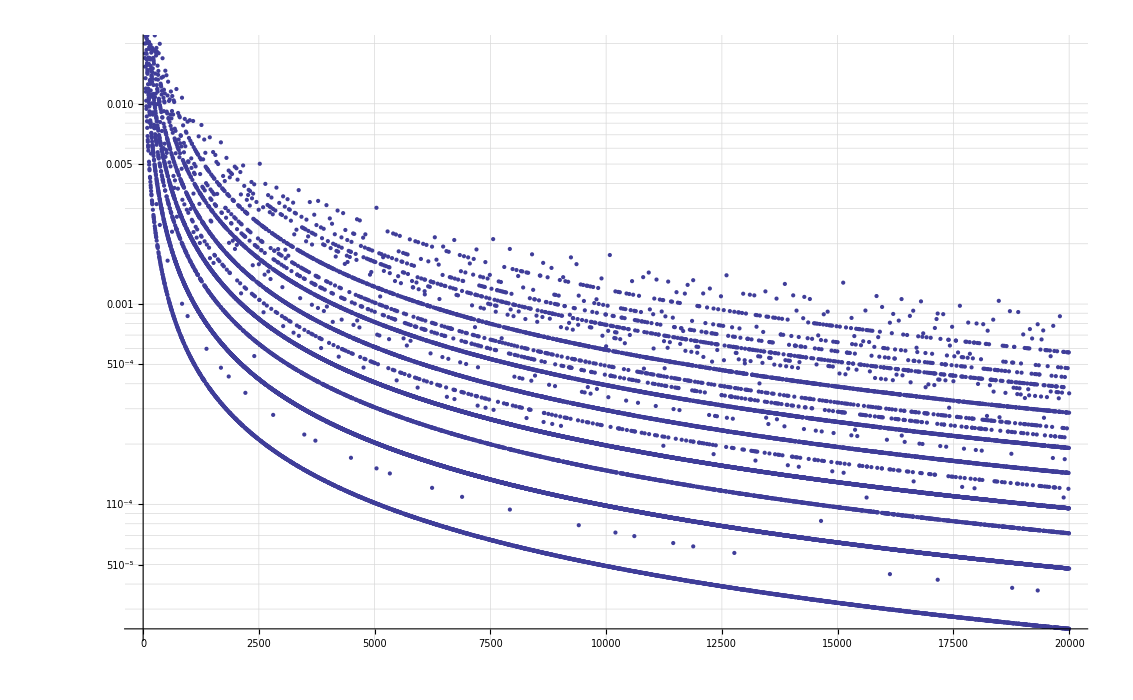

```mathematica
Monitor[ListLogPlot[Table[DivisorSigma[0,i]/(HarmonicNumber[i]+Exp[HarmonicNumber[i]]*Log[HarmonicNumber[i]]),{i,1,20000}],
GridLines->Automatic,
PlotRange->{All,{0,1}}],i]
```

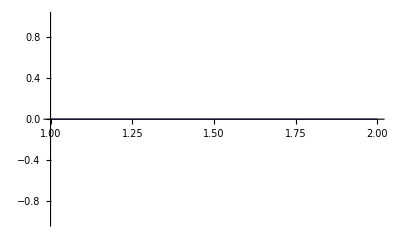

```mathematica
ListLinePlot[Table[{x,((x - 2)*(3*x + 2)*(x*(x + 15) + 20)*Binomial[4, (x - 2)/x])/((-1)^(2/x)*(72*x^4))},{x,1,100}]]
```

```mathematica
ListPlot[Table[{x,(((x+1) (x+2))/(6 x^2) ((-1)^(-2/x) (x+2) (3 x-2) ((x-15) x+20) Binomial[4, 3-2/x])/(72 x^4)-((x-2) (x-1))/(6 x^2) ((-1)^(-2/x) (x-2) (3 x+2) (x (x+15)+20) Binomial[4, (x-2)/x])/(72 x^4))/(-((x+1) (x+2))/(6 x^2) ((-1)^(-2/x) (x^4-11 x^2+10) Binomial[4, 2-2/x])/(9 x^4) ((-1)^(-1/x) (x-8) x sin(π/x))/(3 π (2 x-1))+(2/3-2/(3 x^2)) ((-1)^(-2/x) (x-2) (3 x+2) (x (x+15)+20) Binomial[4, (x-2)/x])/(72 x^4) ((-1)^(-1/x) (x-8) x sin(π/x))/(3 π (2 x-1))+((x-2) (x-1))/(6 x^2) ((-1)^(-2/x) (x^4-11 x^2+10) Binomial[4, 2-2/x])/(9 x^4) ((-1)^(-1/x) x (x+8) sin(π/x))/(3 (2 π x+π))-(2/3-2/(3 x^2)) ((-1)^(-2/x) (x+2) (3 x-2) ((x-15) x+20) Binomial[4, 3-2/x])/(72 x^4) ((-1)^(-1/x) x (x+8) sin(π/x))/(3 (2 π x+π))+((x+1) (x+2))/(6 x^2) ((-1)^(-2/x) (x+2) (3 x-2) ((x-15) x+20) Binomial[4, 3-2/x])/(72 x^4) (2 (-1)^(-1/x) x (x^2-4) sin(π/x))/(3 π (x^2-1))-((x-2) (x-1))/(6 x^2) ((-1)^(-2/x) (x-2) (3 x+2) (x (x+15)+20) Binomial[4, (x-2)/x])/(72 x^4) (2 (-1)^(-1/x) x (x^2-4) sin(π/x))/(3 π (x^2-1)))},{x,-100,0,1/3}],Joined->True]
```

Power::infy: Infinite expression 1/0 encountered.

∞::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power will be suppressed during this calculation.

∞::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of indet will be suppressed during this calculation.

-Graphics-

```mathematica
Det[With[
{m=3,b=x},
Table[TraditionalForm[FullSimplify[Fred2[i,j,b,m]]],{i,0,m-1},{j,0,m-1}]
]]
```

-((x+1) (x+2))/(6 x^2) ((-1)^(-2/x) (x^4-11 x^2+10) Binomial[4, 2-2/x])/(9 x^4) ((-1)^(-1/x) (x-8) x sin(π/x))/(3 π (2 x-1))+(2/3-2/(3 x^2)) ((-1)^(-2/x) (x-2) (3 x+2) (x (x+15)+20) Binomial[4, (x-2)/x])/(72 x^4) ((-1)^(-1/x) (x-8) x sin(π/x))/(3 π (2 x-1))+((x-2) (x-1))/(6 x^2) ((-1)^(-2/x) (x^4-11 x^2+10) Binomial[4, 2-2/x])/(9 x^4) ((-1)^(-1/x) x (x+8) sin(π/x))/(3 (2 π x+π))-(2/3-2/(3 x^2)) ((-1)^(-2/x) (x+2) (3 x-2) ((x-15) x+20) Binomial[4, 3-2/x])/(72 x^4) ((-1)^(-1/x) x (x+8) sin(π/x))/(3 (2 π x+π))+((x+1) (x+2))/(6 x^2) ((-1)^(-2/x) (x+2) (3 x-2) ((x-15) x+20) Binomial[4, 3-2/x])/(72 x^4) (2 (-1)^(-1/x) x (x^2-4) sin(π/x))/(3 π (x^2-1))-((x-2) (x-1))/(6 x^2) ((-1)^(-2/x) (x-2) (3 x+2) (x (x+15)+20) Binomial[4, (x-2)/x])/(72 x^4) (2 (-1)^(-1/x) x (x^2-4) sin(π/x))/(3 π (x^2-1))